## Hamiltonians

### Definitions

The Harper model involves an on site potential V_i(λ,α,ϕ)=2λ cos(2π α i+ϕ). Here we mostly take λ=1. This is because when λ>1 the spectrum is pure point, and when λ<1 the spectrum is absolutely continuous. Only at λ=1 is the spectrum singular continuous (and interesting !).

```mathematica
(* Harper *)
hharp[p_,q_,ϕ_,λ_]:=Block[{hopping,pot},(*hopping subdiagonal part*)hopping=Table[{i,i+1}->-1.,{i,q-1}];
(*periodic boundary conditions*)AppendTo[hopping,{1,q}->-1.];
(*convert to matrix*)hopping=SparseArray[hopping,{q,q}];
(*symmetrize*)hopping=hopping+Transpose[hopping];
(*diagonal part*)pot=SparseArray[Table[{i,i}->2.λ Cos[2 π p i/q+ϕ],{i,q}],{q,q}];
Normal[pot+hopping]]

(*choosing Fibonacci numbers as approximants*)
hfib[n_,ϕ_,λ_]:=hharp[Fibonacci[n-1],Fibonacci[n],ϕ,λ];
SetAttributes[hfib,Listable];
```

```mathematica
(* Harper anti-periodic *)
hharpa[p_,q_,ϕ_,λ_]:=Block[{hopping,pot},(*hopping subdiagonal part*)hopping=Table[{i,i+1}->-1.,{i,q-1}];
(*anti-periodic boundary conditions*)AppendTo[hopping,{1,q}->1.];
(*convert to matrix*)hopping=SparseArray[hopping,{q,q}];
(*symmetrize*)hopping=hopping+Transpose[hopping];
(*diagonal part*)pot=SparseArray[Table[{i,i}->2.λ Cos[2 π p i/q+ϕ],{i,q}],{q,q}];
Normal[pot+hopping]]

(*choosing Fibonacci numbers as approximants*)
hfiba[n_,ϕ_,λ_]:=hharpa[Fibonacci[n-1],Fibonacci[n],ϕ,λ];
SetAttributes[hfiba,Listable];
```

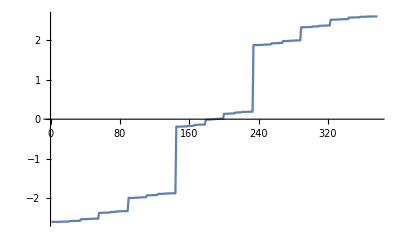

```mathematica
vp=Sort@Eigenvalues[hfib[14,0,1.]];
ListPlot[vp,Joined->True]
```

### Arbitrary precision and λ dependance

For λ>1, the bands rapidly scale towards zero. To give some numbers, for λ=10 and F_n=144, it needs about 50 digits of working precision to accuratly resolve the smallest energy band.
This behaviour is understandable. When λ>1, and in the limit n → ∞, the spectrum is pure point.

```mathematica
(* periodic Harper, arbitrary precision *)
hharp[p_,q_,ϕ_,λ_,wp_]:=Block[{hopping,pot},(*hopping subdiagonal part*)hopping=Table[{i,i+1}->N[-1,wp],{i,q-1}];
(*periodic boundary conditions*)AppendTo[hopping,{1,q}->N[-1,wp]];
(*convert to matrix*)hopping=SparseArray[hopping,{q,q}];
(*symmetrize*)hopping=hopping+Transpose[hopping];
(*diagonal part*)pot=SparseArray[Table[{i,i}->N[2,wp]λ Cos[2 π p i/q-ϕ],{i,q}],{q,q}];
Normal[pot+hopping]]

(*choosing Fibonacci numbers as approximants*)
hfib[n_,ϕ_,λ_,wp_]:=hharp[Fibonacci[n-1],Fibonacci[n],ϕ,N[λ,wp],wp];
SetAttributes[hfib,Listable];
```

```mathematica
(* anti-periodic Harper, arbitrary precision *)
hharpa[p_,q_,ϕ_,λ_,wp_]:=Block[{hopping,pot},(*hopping subdiagonal part*)hopping=Table[{i,i+1}->N[-1,wp],{i,q-1}];
(*anti-periodic boundary conditions*)AppendTo[hopping,{1,q}->N[1,wp]];
(*convert to matrix*)hopping=SparseArray[hopping,{q,q}];
(*symmetrize*)hopping=hopping+Transpose[hopping];
(*diagonal part*)pot=SparseArray[Table[{i,i}->N[2,wp]λ Cos[2 π p i/q-ϕ],{i,q}],{q,q}];
Normal[pot+hopping]]

(*choosing Fibonacci numbers as approximants*)
hfiba[n_,ϕ_,λ_,wp_]:=hharpa[Fibonacci[n-1],Fibonacci[n],ϕ,N[λ,wp],wp];
SetAttributes[hfib,Listable];
```

```mathematica
n=15;
wp=10;
λ=1;
enp=Sort@Eigenvalues[hfib[n,0,λ,wp]];
ena=Sort@Eigenvalues[hfiba[n,0,λ,wp]];
```

```mathematica
Min[Abs[enp-ena]]
```

9.9×10^-7

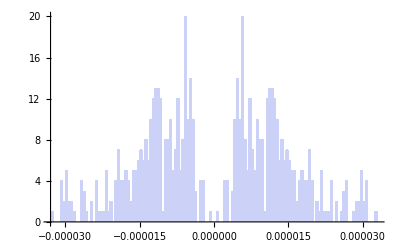

```mathematica
Histogram[ena-enp,100]
```

### Tests

```mathematica
n=14;
ϕ=0;
```

```mathematica
(* wavefunctions in the co-basis, ordered by IDoS label *)
wf=Block[{val,vec,i=n,λ=1.},
{val,vec}=Eigensystem[hfib[i,0,λ]];
(*order wavefunctions by increasing energy*)
vec[[Ordering[val]]]
];
```

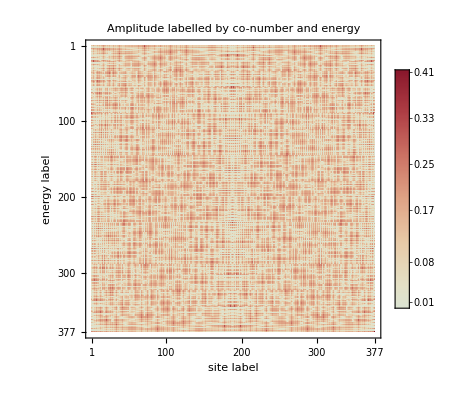

```mathematica
MatrixPlot [Abs[wf]^2,FrameLabel->{"energy label","site label"},PlotLabel->"Amplitude labelled by co-number and energy",PlotLegends->Automatic,ColorFunction->"ThermometerColors"]
```

Reordering the sites by increasing value of the potential (ie classifying them according to their local environment) renders the energy label/position label symmetry evident.

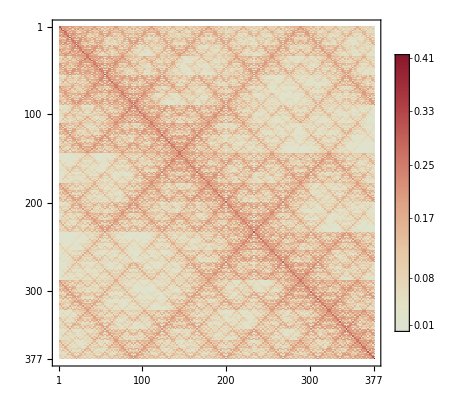

```mathematica
(* reorder wavefunctions by increasing value of the onsite potential *)
ord=Block[{p=Fibonacci[n-1],q=Fibonacci[n],potlist},
potlist=Table[Cos[2π p i/q+ϕ],{i,q}]//N;
Ordering[potlist]
];
(* reorder wavefunctions *)
wford=Table[wf[[i]][[ord]],{i,Fibonacci[n]}];
MatrixPlot [Abs[wford]^2,PlotRange->All,PlotLegends->Automatic,ColorFunction->"ThermometerColors"]
```

Let’s Fourier transform the site-reordered wavefunctions!

```mathematica
wfk=ParallelMap[Fourier,wford];
```

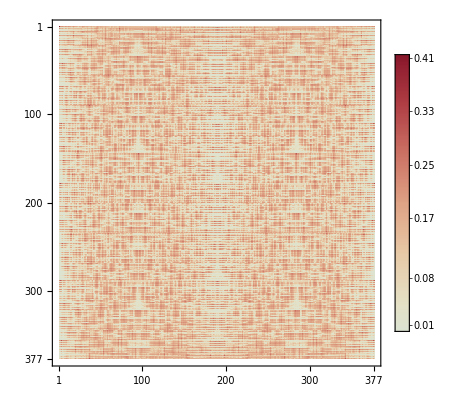

```mathematica
MatrixPlot [Abs[wfk]^2,PlotRange->All,PlotLegends->Automatic,ColorFunction->"ThermometerColors"]
```

## Averaged dimensions

#### Preliminaries (diagonalization, computation of the bands, of the wave vectors...)

```mathematica
(* return bands and intensities ordered by increasing energy, for 2 consecutive sizes Subscript[F, n] and Subscript[F, n+1] *)
IntBands[n_,λ_]:=Block[{nN=n+3,vpp,vpa,vppN,vpaN,wfp,wfa,wfpN,wfaN,o,intensities,intensitiesN,intp,inta,intpN,intaN,bands,bandsN},

(* spectres des systèmes de taille i p et anti-p *)
{vpp,wfp}=Eigensystem[hfib[n,0,λ]];
{vpa,wfa}=Eigensystem[hfiba[n,0,λ]];

o=Ordering[vpp];
vpp=vpp[[o]];
wfp=wfp[[o]];
(* intensity *)
intp=Abs[wfp]^2;

o=Ordering[vpa];
vpa=vpa[[o]];
wfa=wfa[[o]];
inta=Abs[wfa]^2;

intensities=0.5*(intp+inta);

(* spectres des systèmes de taille i+1 p et anti-p *)
{vppN,wfpN}=Eigensystem[hfib[nN,0,λ]];
{vpaN,wfaN}=Eigensystem[hfiba[nN,0,λ]];

o=Ordering[vppN];
vppN=vppN[[o]];
wfpN=wfpN[[o]];
(* intensity *)
intpN=Abs[wfpN]^2;

o=Ordering[vpaN];
vpaN=vpaN[[o]];
wfaN=wfaN[[o]];
intaN=Abs[wfaN]^2;

intensitiesN=0.5*(intpN+intaN);

(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bands=MapThread[Abs[#1-#2]&,{vpa,vpp}];
bandsN=MapThread[Abs[#1-#2]&,{vpaN,vppN}];

{intensities,intensitiesN,bands,bandsN}]
```

In the weak quasiperiodicity limit, Γ^(n+1)/Γ^n rather than Γ^(n+3)/Γ^n.

```mathematica
(* return bands and intensities ordered by increasing energy, for 2 consecutive sizes Subscript[F, n] and Subscript[F, n+1] *)
IntBandsWeak[n_,λ_]:=Block[{nN=n+1,vpp,vpa,vppN,vpaN,wfp,wfa,wfpN,wfaN,o,intensities,intensitiesN,intp,inta,intpN,intaN,bands,bandsN},

(* spectres des systèmes de taille i p et anti-p *)
{vpp,wfp}=Eigensystem[hfib[n,0,λ]];
{vpa,wfa}=Eigensystem[hfiba[n,0,λ]];

o=Ordering[vpp];
vpp=vpp[[o]];
wfp=wfp[[o]];
(* intensity *)
intp=Abs[wfp]^2;

o=Ordering[vpa];
vpa=vpa[[o]];
wfa=wfa[[o]];
inta=Abs[wfa]^2;

intensities=0.5*(intp+inta);

(* spectres des systèmes de taille i+1 p et anti-p *)
{vppN,wfpN}=Eigensystem[hfib[nN,0,λ]];
{vpaN,wfaN}=Eigensystem[hfiba[nN,0,λ]];

o=Ordering[vppN];
vppN=vppN[[o]];
wfpN=wfpN[[o]];
(* intensity *)
intpN=Abs[wfpN]^2;

o=Ordering[vpaN];
vpaN=vpaN[[o]];
wfaN=wfaN[[o]];
intaN=Abs[wfaN]^2;

intensitiesN=0.5*(intpN+intaN);

(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bands=MapThread[Abs[#1-#2]&,{vpa,vpp}];
bandsN=MapThread[Abs[#1-#2]&,{vpaN,vppN}];

{intensities,intensitiesN,bands,bandsN}]
```

```mathematica
(* Averaged q-intensity *)
avInt[intlist_,q_]:=(1/Length[intlist])*Map[Plus@@((#)^q)&,Transpose[intlist]];
```

```mathematica
(* Compute τx(q) from the averaged q-intensity *)
tauqx[avint_,avintN_]:=-Log[(Plus@@avint)/(Plus@@avintN)]/Log[(Length@avint)/(Length@avintN)];
```

```mathematica
(* Compute τμ(q) from 2 consecutive (Subscript[F, n] and Subscript[F, n+3]) averaged q-intensities *)
tauqmu[avint_,avintN_,bl_,blN_]:=Block[{gammu,gammuN},
(* associated Γ function (bl is the list of bands) *)
gammu=Plus@@((avint)(bl)^-τ);
gammuN=Plus@@((avintN)(blN)^-τ);
τ/.FindRoot[gammu/gammuN-1,{τ,1.}]]
```

```mathematica
(* Compute spectral τ(qsp) *)
tauspec[qsp_,bl_,blN_]:=Block[{gamSpec,gamSpecN},
(* Fractal dimension of the spectrum *)
gamSpec=(Length@bl)^-qsp Plus@@((bl)^-τ);
gamSpecN=(Length@blN)^-qsp Plus@@((blN)^-τ);

τ/.FindRoot[gamSpecN/gamSpec-1,{τ,0.5}]
]
```

#### Focus on τmu

```mathematica
qr=Range[0.1,10.,.34];
ρ=0.9;
```

```mathematica
n=13;
{int,intN,bl,blN}=IntBands[n,ρ];
avints=ParallelMap[avInt[int,#]&,qr];
avintsN=ParallelMap[avInt[intN,#]&,qr];
τmulist13=Parallelize@MapThread[tauqmu[#1,#2,bl,blN]&,{avints,avintsN}];
```

```mathematica
n=16;
{int,intN,bl,blN}=IntBands[n,ρ];
avints=ParallelMap[avInt[int,#]&,qr];
avintsN=ParallelMap[avInt[intN,#]&,qr];
τmulist16=Parallelize@MapThread[tauqmu[#1,#2,bl,blN]&,{avints,avintsN}];
```

```mathematica
n=13;
{int,intN,bl,blN}=IntBandsWeak[n,ρ];
avints=ParallelMap[avInt[int,#]&,qr];
avintsN=ParallelMap[avInt[intN,#]&,qr];
τmulist13W=Parallelize@MapThread[tauqmu[#1,#2,bl,blN]&,{avints,avintsN}];
```

```mathematica
n=16;
{int,intN,bl,blN}=IntBandsWeak[n,ρ];
avints=ParallelMap[avInt[int,#]&,qr];
avintsN=ParallelMap[avInt[intN,#]&,qr];
τmulist16W=Parallelize@MapThread[tauqmu[#1,#2,bl,blN]&,{avints,avintsN}];
```

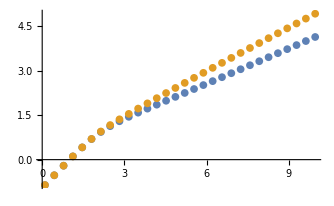

```mathematica
ListPlot[glue[qr,#]&/@{τmulist13,τmulist16},PlotRange->All]
```

```mathematica
Plus@@((τmulist13-τmulist16)^2)
```

5.47375

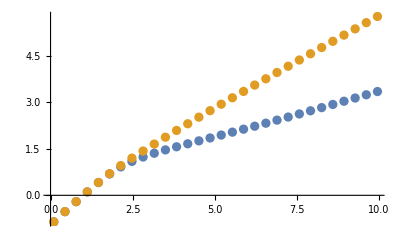

```mathematica
ListPlot[glue[qr,#]&/@{τmulist13W,τmulist16W},PlotRange->All]
```

```mathematica
τth[q_]:=If[q<2,q-1,q/2];
```

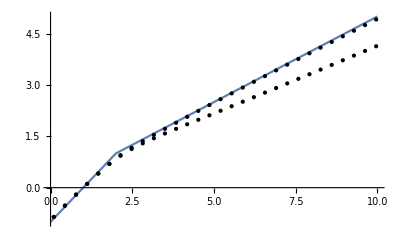

```mathematica
Plot[τth[q],{q,0,10},Epilog->{Point@glue[qr,τmulist13],Point@glue[qr,τmulist16]}]
```

#### Focus on τx

```mathematica
qr=Range[0.1,10.,.34];
ρ=0.9;
```

```mathematica
n=13;
{int,intN,bl,blN}=IntBands[n,ρ];
avints=ParallelMap[avInt[intN,#]&,qr];
τxlist13=ParallelMap[tauqx,avints];
```

```mathematica
n=16;
{int,intN,bl,blN}=IntBands[n,ρ];
avints=ParallelMap[avInt[intN,#]&,qr];
τxlist14=ParallelMap[tauqx,avints];
```

```mathematica
n=13;
{int,intN,bl,blN}=IntBandsWeak[n,ρ];
avints=ParallelMap[avInt[intN,#]&,qr];
τxlist13W=ParallelMap[tauqx,avints];
```

```mathematica
n=16;
{int,intN,bl,blN}=IntBandsWeak[n,ρ];
avints=ParallelMap[avInt[intN,#]&,qr];
τxlist14W=ParallelMap[tauqx,avints];
```

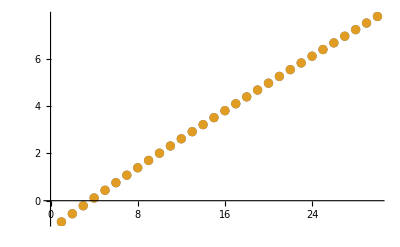

```mathematica
ListPlot[{τxlist13,τxlist14}]
```

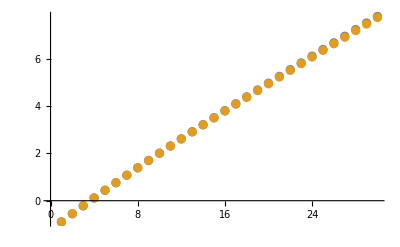

```mathematica
ListPlot[{τxlist14,τxlist14W}]
```

#### Focus on τspec

```mathematica
qr=Range[0.1,10.,.34];
```

```mathematica
n=13;
{int,intN,bl,blN}=IntBandsWeak[n,λ];
τspeclist1=ParallelMap[{#,tauspec[#,bl,blN]}&,qr];
```

```mathematica
n=16;
{int,intN,bl,blN}=IntBandsWeak[n,λ];
τspeclist2=ParallelMap[{#,tauspec[#,bl,blN]}&,qr];
```

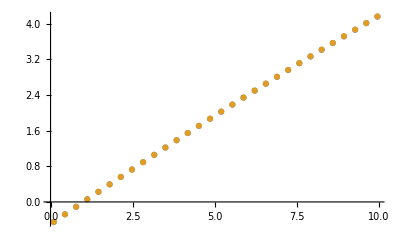

```mathematica
ListPlot[{τspeclist1,τspeclist2}]
```

#### Comparison: n_new = n+1: λ=10

```mathematica
λ=1.;
n=13;
nN=n+3;
qr=Range[.1,10.,.2];
```

```mathematica
(* bands, intensities... *)
{int,intN,bl,blN}=IntBands[n,λ];
```

```mathematica
{int2,intN2,bl2,blN2}=IntBands[nN,λ];
```

```mathematica
(* list of averaged over i and weighted intensities *)
avints=ParallelMap[avInt[int,#]&,qr];
avintsN=ParallelMap[avInt[intN,#]&,qr];
```

```mathematica
(* list of averaged over i and weighted intensities *)
avints2=ParallelMap[avInt[int2,#]&,qr];
avintsN2=ParallelMap[avInt[intN2,#]&,qr];
```

```mathematica
(* τx(qr) *)
τx1=Parallelize@MapThread[tauqx,{avints,avintsN}];
τx2=Parallelize@MapThread[tauqx,{avints2,avintsN2}];
(* deduce qspec *)
qsp1=1+τx1;
qsp2=1+τx2;
```

```mathematica
(* compute τ(qspec) *)
τsp1=ParallelMap[tauspec[#,bl,blN]&,qsp1];
τsp2=ParallelMap[tauspec[#,bl2,blN2]&,qsp2];
```

```mathematica
(* compute τμ(qr) *)
τmu1=Parallelize@MapThread[tauqmu[#1,#2,bl,blN]&,{avints,avintsN}];
τmu2=Parallelize@MapThread[tauqmu[#1,#2,bl2,blN2]&,{avints2,avintsN2}];
```

```mathematica
(* compare Dμ(qr) and Dx(qr)*D(qspec) = τ(qspec)/(qr-1) *)
dxdsp1=τsp1/(qr-1);
dxdsp2=τsp2/(qr-1);
dmu1=τmu1/(qr-1);
dmu2=τmu2/(qr-1);
```

```mathematica
glue[l1_,l2_]:=MapThread[{#1,#2}&,{l1,l2}];
```

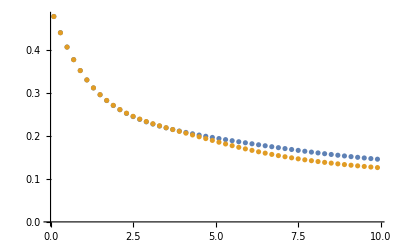

```mathematica
ListPlot[{glue[qr,dxdsp1],glue[qr,dmu1]}]
```

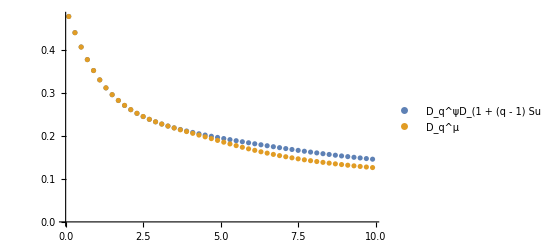

```mathematica
ListPlot[{glue[qr,dxdsp2],glue[qr,dmu2]},PlotLegends->{"D_q^ψD_(1 + (q - 1) SuperscriptBox[SubscriptBox[D, q], ψ])","D_q^μ"}]
```

```mathematica
Export[NotebookDirectory[]<>"data/spectrum_wf_relation.pdf",%]
```

/home/nicolas/git/spectrum_quasicrystals/Harper/data/spectrum_wf_relation.pdf

#### Comparison: n_new = n+3: ρ=0.9

```mathematica
ρ=0.9;
n=13;
nN=n+3;
qr=Range[.1,10.,.2];
```

```mathematica
(* bands, intensities... *)
{int,intN,bl,blN}=IntBands[n,ρ];
```

```mathematica
{int2,intN2,bl2,blN2}=IntBands[nN,ρ];
```

```mathematica
(* list of averaged over i and weighted intensities *)
avints=ParallelMap[avInt[int,#]&,qr];
avintsN=ParallelMap[avInt[intN,#]&,qr];
```

```mathematica
(* list of averaged over i and weighted intensities *)
avints2=ParallelMap[avInt[int2,#]&,qr];
avintsN2=ParallelMap[avInt[intN2,#]&,qr];
```

```mathematica
(* τx(qr) *)
τx19=Parallelize@MapThread[tauqx,{avints,avintsN}];
τx29=Parallelize@MapThread[tauqx,{avints2,avintsN2}];
(* deduce qspec *)
qsp19=1+τx19;
qsp29=1+τx29;
```

```mathematica
(* compute τ(qspec) *)
τsp19=ParallelMap[tauspec[#,bl,blN]&,qsp19];
τsp29=ParallelMap[tauspec[#,bl2,blN2]&,qsp29];
```

```mathematica
(* compute τμ(qr) *)
τmu19=Parallelize@MapThread[tauqmu[#1,#2,bl,blN]&,{avints,avintsN}];
τmu29=Parallelize@MapThread[tauqmu[#1,#2,bl2,blN2]&,{avints2,avintsN2}];
```

```mathematica
(* compare Dμ(qr) and Dx(qr)*D(qspec) = τ(qspec)/(qr-1) *)
dxdsp19=τsp19/(qr-1);
dxdsp29=τsp29/(qr-1);
dmu19=τmu19/(qr-1);
dmu29=τmu29/(qr-1);
```

```mathematica
glue[l1_,l2_]:=MapThread[{#1,#2}&,{l1,l2}];
```

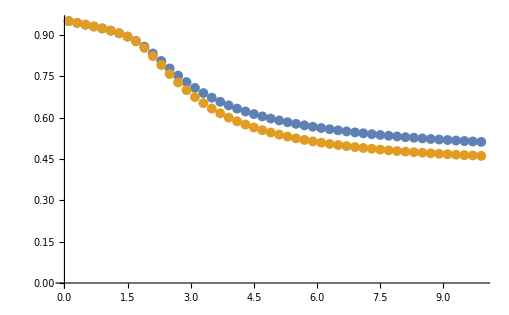

```mathematica
ListPlot[{glue[qr,dxdsp19],glue[qr,dmu19]}]
```

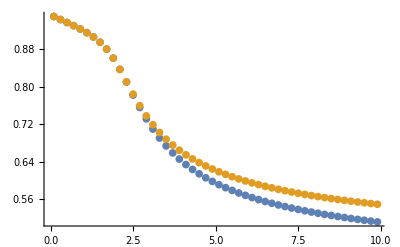

```mathematica
ListPlot[{glue[qr,dxdsp29],glue[qr,dmu29]}]
```

```mathematica
dthper[q_]:=If[q<2,1-(1-ρ)4 Pi^-2,q/(2(q-1))];
```

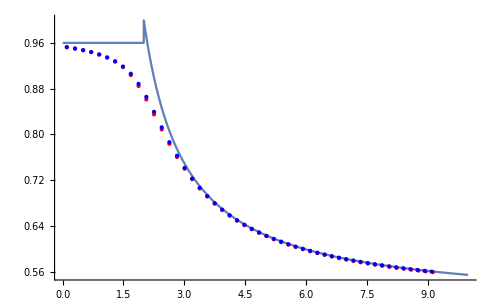

```mathematica
Plot[dthper[q],{q,0,10},Epilog->{{Red,Point@glue[qsp19,τsp19/(qsp19-1)]},{Blue,Point@glue[qsp29,τsp29/(qsp29-1)]}}]
```

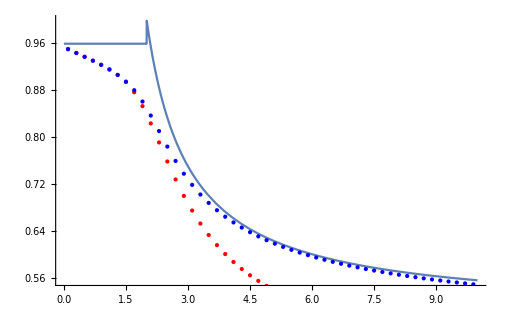

```mathematica
Plot[dthper[q],{q,0,10},Epilog->{{Red,Point@glue[qr,τmu19/(qr-1)]},{Blue,Point@glue[qr,τmu29/(qr-1)]}}]
```

#### Comparison: n_new = n+1

```mathematica
ρ=0.9;
n=13;
nN=n+3;
qr=Range[.1,10.,.2];
```

```mathematica
(* bands, intensities... *)
{int,intN,bl,blN}=IntBandsWeak[n,ρ];
```

```mathematica
{int2,intN2,bl2,blN2}=IntBandsWeak[nN,ρ];
```

```mathematica
(* list of averaged over i and weighted intensities *)
avints=ParallelMap[avInt[int,#]&,qr];
avintsN=ParallelMap[avInt[intN,#]&,qr];
```

```mathematica
(* list of averaged over i and weighted intensities *)
avints2=ParallelMap[avInt[int2,#]&,qr];
avintsN2=ParallelMap[avInt[intN2,#]&,qr];
```

```mathematica
(* τx(qr) *)
τx1w=tauqx/@avintsN;
τx2w=tauqx/@avintsN2;
(* deduce qspec *)
qsp1w=1+τx1w;
qsp2w=1+τx2w;
```

```mathematica
(* compute τ(qspec) *)
τsp1w=ParallelMap[tauspec[#,bl,blN]&,qsp1w];
τsp2w=ParallelMap[tauspec[#,bl2,blN2]&,qsp2w];
```

```mathematica
(* compute τμ(qr) *)
τmu1w=Parallelize@MapThread[tauqmu[#1,#2,bl,blN]&,{avints,avintsN}];
τmu2w=Parallelize@MapThread[tauqmu[#1,#2,bl2,blN2]&,{avints2,avintsN2}];
```

```mathematica
(* compare Dμ(qr) and Dx(qr)*D(qspec) = τ(qspec)/(qr-1) *)
dxdsp1w=τsp1w/(qr-1);
dxdsp2w=τsp2w/(qr-1);
dmu1w=τmu1w/(qr-1);
dmu2w=τmu2w/(qr-1);
```

```mathematica
glue[l1_,l2_]:=MapThread[{#1,#2}&,{l1,l2}];
```

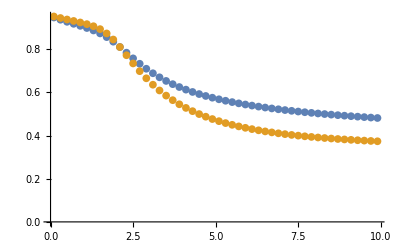

```mathematica
ListPlot[glue[qr,#]&/@{dxdsp1w,dmu1w}]
```

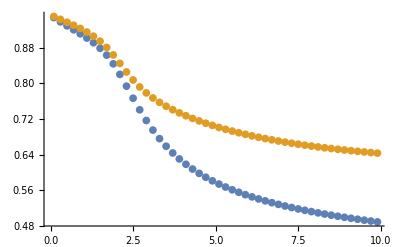

```mathematica
ListPlot[glue[qr,#]&/@{dxdsp2w,dmu2w}]
```

```mathematica
Plus@@((dxdsp1-dmu1)^2)
```

0.370558

```mathematica
Plus@@((dxdsp2-dmu2)^2)
```

0.639219

#### τmu by box counting

Compute generalized dimensions by box-counting

```mathematica
(* take a fractal set (represented as an ordered list of points between 0 and 1 each associated to a weight), return qnorm = Subscript[Σ, i] Subscript[p, i]^q, where Subscript[p, i] is the weight of the i^th box. Explicitely, Subscript[p, i] is the sum of the weights of the pts in the i^th box: Subscript[p, i] = Subscript[Σ, s∈Subscript[b, i]] Subscript[w, s].*)
Clear[WeightedBc];
WeightedBc[pts_,weights_,n_,δ_,q_]:=Block[{curLbl=1,curBS=0,Δ,b=δ^-n,qnorm=0,ntot=Length[pts],curweight=0,len=Length[pts],loop,p0},
p0=pts[[curLbl]];
(*Δ:distance btw the left side of the current box and the current pt*)
(*If[b≥p0,Δ=b-p0,Δ=Mod[p0,b]];*)
Δ=Max[b-p0,0];
(* position of the current box left side *)
curBS=p0-Δ;
While[curLbl≤len,
(* there is for now 0 pt in the current box *)
curweight=0;
(*while the current pt is in the current box, add its weight and pass to the pt on its right*)
While[Δ≤b,
curweight+=weights[[curLbl]];
curLbl++;
If[curLbl≤ len,Δ=pts[[curLbl]]-curBS,Break[]];
];
(* Subscript[p, i]^q *)
qnorm+=(curweight)^q;
If[curLbl>len,Break[]];
(*after the loop the current box has jumped of Floor[Δ/b] units*)
curBS+=b Floor[Δ/b];
Δ=pts[[curLbl]]-curBS;
];
Return[qnorm];]
```

```mathematica
(* To do. *)
(* μ: measure of probability: μ[[i]]={position of pt i, probability weight of pt i} *)
Clear[WeightedBc];
WeightedBc[μ_,n_,δ_,q_]:=Block[{curLbl=1,curBS=0,Δ,b=δ^-n,qnorm=0,ntot=Length[pts],curweight=0,len=Length[pts],loop,p0},
Return[qnorm];]
```

Average qnorm over some possible origins of the boxes. This is equivalent to making the whole data set rotate, and to average over some possible rotations.

```mathematica
(* "rotate" the 1 pt (0≤pt≤1) or a list of pts by t *)
Clear[rot];
rot[pt_,t_]:=If[pt≥t,pt-t,pt-t+1];
SetAttributes[rot,Listable];
```

```mathematica
Manipulate[ListPlot[{sp,rot[sp,r]},PlotRange->All],{r,0,1}]
```

```mathematica
AveragedBc[pts_,weights_,n_,δ_,q_,rotstep_]:=Block[{len=Length[pts],nrots,avqnorm=0,ptsN,weightsN,o},
If[Mod[rotstep^-1,1]≠ 0,Break[];Throw["The rotation step is uncommensurable with the number of pts in the data set."]];
nrots=IntegerPart[1/rotstep];
For[i=0,i<nrots,i++,
(* rotate the whole set of points *)
ptsN=rot[pts,i rotstep];
(* the points must be reordered by increasing position; compute the permutation that does that *)
o=Ordering[ptsN];
(* reorder the points and the associated weights *)
ptsN=ptsN[[o]];
weightsN=weights[[o]];
avqnorm+=WeightedBc[ptsN,weightsN,n,δ,q]];
avqnorm/nrots
]
```

For τ^(μ,i), the point E_a weights |ψ_(i,a)|^2.

```mathematica
intE[n_,ρ_,k_]:=Block[{ts=1.,tw=ρ,vpp,vpa,wfp,wfa,o,intp,inta},
(* spectres des systèmes de taille i p et anti-p *)
{vpp,wfp}=Eigensystem[hk[k,n-2,tw,ts]];

o=Ordering[vpp];
vpp=vpp[[o]];
wfp=wfp[[o]];
(* intensity *)
intp=Abs[wfp]^2;

(* rescale spectrum between 0 and 1 *)
vpp=(vpp-vpp[[1]])/(vpp[[-1]]-vpp[[1]]);

{intp,vpp}
]
```

```mathematica
n=16;
ρ=.5;
{intp,sp}=intE[n,ρ,0.];
{inta,sp}=intE[n,ρ,Pi];
(* w[[i]] is the set of weights for τ^(μ,i) *)
wp=Transpose[intp];
wa=Transpose[inta];
```

```mathematica
Fibonacci[16]/2//N
```

493.5

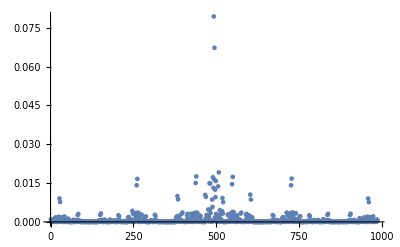

```mathematica
ListPlot[wp[[493]],PlotRange->All]
```

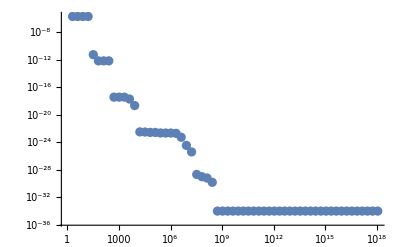

```mathematica
i=494;
q=20.;
r=Range[1,60,1.];
delta=2.;
(* compute the number of filled boxes for a whole range of values of n *)
nb=ParallelMap[WeightedBc[sp,wp[[i]],#,delta,q]&,r];
(*number of filled boxes as a function of their length*)
dat2=Parallelize@MapThread[{#1,#2}&,{delta^r,nb}];
(* the slope is the box-counting dimension of the spectrum *)
ListLogLogPlot[{dat2},PlotRange->All]
```

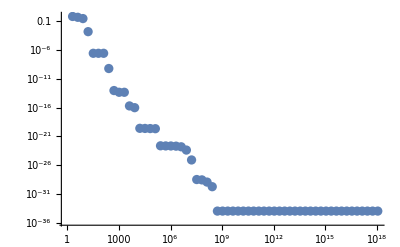

```mathematica
r=Range[1,60,1.];
delta=2.;
(* compute the number of filled boxes for a whole range of values of n *)
nb2=ParallelMap[AveragedBc[sp,wp[[i]],#,delta,q,0.1]&,r];
(*number of filled boxes as a function of their length*)
dat3=Parallelize@MapThread[{#1,#2}&,{delta^r,nb2}];
(* the slope is the box-counting dimension of the spectrum *)
ListLogLogPlot[{dat3},PlotRange->All]
```

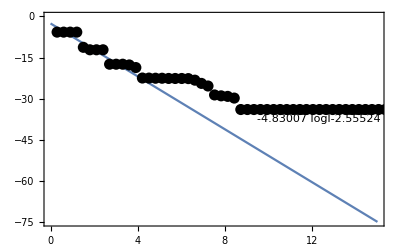

```mathematica
(* now we can fit the slope to get the box-counting dimension *)
xi=1;xf=xi+9;
fit=LinearModelFit[Log10@dat2[[xi;;xf]],logl,logl];
Plot[Normal@fit,{logl,0,15},Axes->False,Frame->True,Epilog->{PointSize@.02,Point@Log10@dat2},PlotLegends->Placed[Normal@fit,{Right,Center}]]
```

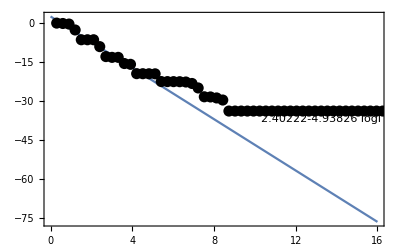

```mathematica
(* now we can fit the slope to get the box-counting dimension *)
xi=1;xf=xi+12;
fit=LinearModelFit[Log10@dat3[[xi;;xf]],logl,logl];
Plot[Normal@fit,{logl,0,16},Axes->False,Frame->True,Epilog->{PointSize@.02,Point@Log10@dat3},PlotLegends->Placed[Normal@fit,{Right,Center}]]
```

#### Δχ^μ

```mathematica
(* take a renormalization path (seq), a site label (i) and an approximant size (n) and return the new renormalization path, the new site label and the new size after one renormalization group operation *)
ClearAll[i,n];
iterSeq[{seq_,i_,n_}]:=Block[{inew=i,seqn=seq,nnew=n},
If[i>Fibonacci[n-1],seqn="m"<>seq;inew=i-Fibonacci[n-1];nnew=n-2;,
If[i>Fibonacci[n-2],seqn="a"<>seq;inew=i-Fibonacci[n-2];nnew=n-3,
seqn="m"<>seq;nnew=n-2;]];
{seqn,inew,nnew}
]
```

```mathematica
(* false when n<3 *)
test=#[[3]]≥3&;
(* variant where we forget about the site number *)
path[i_,n_]:=NestWhile[iterSeq,{"",i,n},test][[1]]
(* variant where we forget about the site number *)
xPath[i_,n_]:=StringCount[NestWhile[iterSeq,{"",i,n},test][[1]],"m"]
(* variant where we forget about the site number, and compute nx rather than x *)
tree[n_]:= xPath[#,n]&/@ Range[Fibonacci[n]]
(* Display all the paths for a system size *)
paths[n_]:=path[#,n]&/@Range[Fibonacci[n]]
```

Intensity at leading order:
there is intensity only at positions whose renormalization path matches the one of the corresponding energy level.

```mathematica
n=16;
t=tree[n];
p=paths[n];
Table[({#,a}->2^(-t[[#]]))&/@Flatten[Position[p,p[[a]]]],{a,Fibonacci[n]}]//Flatten;
(* intensity at leading order: Subscript[w0, i,a] = |Subscript[ψ, i,a]^(0)|^2 *)
w0=SparseArray[%,{Fibonacci[n],Fibonacci[n]}];
MatrixPlot[w0,ColorFunction->"ThermometerColors",PlotLegends->Automatic]
```

-Graphics-

Check that χ^(0)(q;i) gives the right asymptotic values D_q^(0)(i)

```mathematica
n=16;
ρ=.1;
{int,sp}=intE[n,ρ,0.];
(* w[[i]] is the set of weights for τ^(μ,i) *)
w=Transpose[int];
```

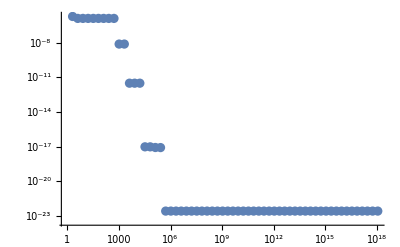

```mathematica
i=89;
q=20.;
r=Range[1,60,1.];
delta=2.;
(* compute the number of filled boxes for a whole range of values of n *)
nb2=ParallelMap[WeightedBc[sp,w[[i]],#,delta,q]&,r];
(*number of filled boxes as a function of their length*)
dat3=Parallelize@MapThread[{#1,#2}&,{delta^r,nb2}];
(* the slope is the box-counting dimension of the spectrum *)
ListLogLogPlot[{dat3},PlotRange->All]
```

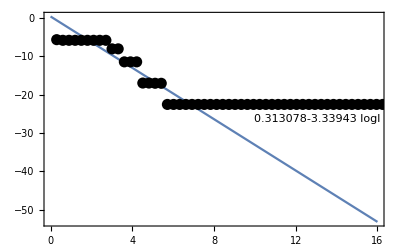

D_q^Box=0.17576 D_q^(0)=0.180907

```mathematica
(* now we can fit the slope to get the box-counting dimension *)
xi=3;xf=xi+16;
fit=LinearModelFit[Log10@dat3[[xi;;xf]],logl,logl];
Plot[Normal@fit,{logl,0,16},Axes->False,Frame->True,Epilog->{PointSize@.02,Point@Log10@dat3},PlotLegends->Placed[Normal@fit,{Right,Center}]]

(* Hölder exponent of the spectrum, α *)
om=1/GoldenRatio;
z=ρ/2;barz=ρ^2;
α[x_]:=Log[om]/(x Log[z]+(1-2x)/3Log[barz]);
(* renormalization path of the site *)
x=t[[i]]/n;
(* local dimension of the wavefunctions at site i *)
Dqx=x Log[2]/Log[Fibonacci[n]^(1/n)];
(* second order contribution *)
ΔDqx=q/(q-1)(4-5 x)/6 ρ^2/Log[Fibonacci[n]^(1/n)];
(* comparison with asymptotics *)
Print["D_q^Box=",Abs[fit[[1,2,2]]]/(q-1)," D_q^(0)=",(Dqx+ΔDqx) α[x]//N]
```

Compute fractal dimensions at fixed q, for every site.
Note that some tests should be ran before executing listdmu in order to determine the right range of boxes lengths r, a good scaling exponent δ for the boxes, and the good range [xi,xf] on which to estimate the slope of Log χ.

```mathematica
glue[l1_,l2_]:=MapThread[{#1,#2}&,{l1,l2}];
```

```mathematica
listdmu[spectrum_,weights_,q_]:=Block[{r=Range[1,60,1.],δ=2.,xi=5,xf,χib,τi,len=Length[spectrum]},
xf=xi+20;
(* χ as a function of the site i and of the boxes length b *)
χib=Table[glue[δ^r,ParallelMap[WeightedBc[spectrum,weights[[i]],#,δ,q]&,r]],{i,len}];
(* τ as a function of the site i *)
τi=ParallelTable[LinearModelFit[Log10@χib[[i,xi;;xf]],logl,logl][[1,2,2]],{i,len}];
(* return Subscript[D, q](i) *)
τi/(q-1)
]
```

```mathematica
dtest=listdmu[sp,w,2.];
```

```mathematica
dth=Block[{t,x,Dqx,ΔDqx},
t=tree[n];
(* renormalization path of the site *)
x=t/n;
(* local dimension of the wavefunctions at site i *)
Dqx=x Log[2]/Log[Fibonacci[n]^(1/n)];
(* second order contribution *)
ΔDqx=q/(q-1)(4-5 x)/6 ρ^2/Log[Fibonacci[n]^(1/n)];
(Dqx+ΔDqx) (α/@x)
];
```

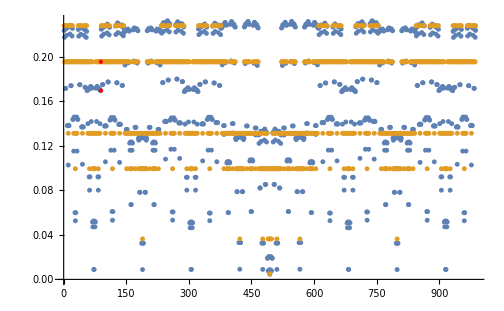

```mathematica
i=89;
ListPlot[{-dtest,dth},PlotRange->All,Epilog->{Red,Point[{i,-dtest[[i]]}],Point[{i,dth[[i]]}]}]
```

```mathematica
Clear[dth]
```

```mathematica
t=tree[n];
tvals=DeleteDuplicates[t];
(* list all positions by increasing value of x *)
listPos=Flatten[Position[t,#]]&/@tvals;
(* for each value of x compute the average - on positions corresponding to this x - fractal dimension *)
avDmu=Mean[-dtest[[#]]]&/@listPos;
(* return the average fractal dimension as a function of x *)
avDmu=MapThread[{#1,#2}&,{tvals/n,avDmu}];
```

```mathematica
(* theoretical values *)
Clear[x];
(* local dimension of the wavefunctions at site i *)
Dqx=x Log[2]/Log[Fibonacci[n]^(1/n)];
(* second order contribution *)
ΔDqx=q/(q-1)(4-5 x)/6 ρ^2/Log[Fibonacci[n]^(1/n)];
dth=(Dqx-ΔDqx) α[x];
d0=Dqx α[x];
```

```mathematica
dth
```

-((0.00786661 (4-5 x)+(14 x Log[2])/Log[377]) Log[GoldenRatio])/(-1.53506 (1-2 x)-2.99573 x)

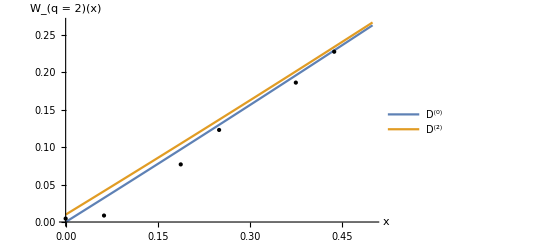

```mathematica
Plot[{asymD[x,n-2]α[x],WfDTh3[n-2,x,q,ρ]α[x]},{x,0,1/2},Epilog->Point@avDmu,PlotRange->All,AxesLabel->{"x","W_(q = 2)(x)"},PlotLegends->{"D^(0)","D^(2)"}]
```

```mathematica
Export[dir<>"img/spectral_local.png",%]
```

/home/nicolas/git/spectrum_quasicrystals/Fibonacci/img/spectral_local.png

Δχ = χ(q;i)-χ^(0)(q;i)=(Σ_b(Σ_(a∈b)|ψ_(i,a)|^2))^q-(Σ_b(Σ_(a∈b)|(ψ_(i,a))^(0)|^2))^q

```mathematica
n=16;
ρ=.1;
{int,sp}=intE[n,ρ,0.];
(* w[[i]] is the set of weights for τ^(μ,i) *)
w=Transpose[int];
```

```mathematica
t=tree[n];
p=paths[n];
Table[({#,a}->2.^(-t[[#]]))&/@Flatten[Position[p,p[[a]]]],{a,Fibonacci[n]}]//Flatten;
(* intensity at leading order: Subscript[w0, i,a] = |Subscript[ψ, i,a]^(0)|^2 *)
w0=SparseArray[%,{Fibonacci[n],Fibonacci[n]}];
```

```mathematica
μ0=MapThread[{#1,#2}&,{sp,#}]&/@w0;
```

```mathematica
Dimensions[μ0[[1]]]
```

{987,2}

```mathematica
ListContourPlot[μ0,PlotRange->All]
```

No more memory available.
Mathematica kernel has shut down.
Try quitting other applications and then retry.

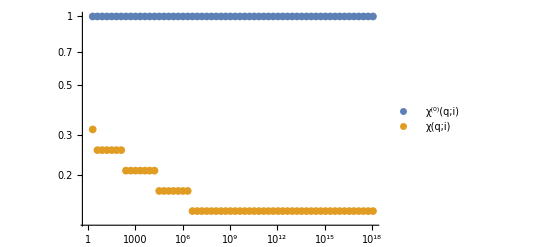

```mathematica
i=494;
q=20.;
r=Range[1,60,1.];
delta=2.;
(* compute the number of filled boxes for a whole range of values of n *)
chi0=ParallelMap[WeightedBc[sp,w0[[i]],#,delta,q]&,r];
chi=ParallelMap[WeightedBc[sp,w[[i]],#,delta,q]&,r];
(*number of filled boxes as a function of their length*)
dat0=Parallelize@MapThread[{#1,#2}&,{delta^r,chi0}];
dat=Parallelize@MapThread[{#1,#2}&,{delta^r,chi}];
(* the slope is the box-counting dimension of the spectrum *)
ListLogLogPlot[{dat0,dat},PlotRange->All,PlotLegends->{"χ^(0)(q;i)","χ(q;i)"}]
Δchi=(chi-chi0);
Δchi=delta^(r (q-1) Dq0)Δchi;
Δdat=Parallelize@MapThread[{#1,#2}&,{delta^r,Δchi}];
(*ListPlot[Δdat,PlotRange->All]*)
(* compute asymptotics Subscript[D, q]^(0)(i) *)
om=1/GoldenRatio;
z=ρ/2;barz=ρ^2;
α[x_]:=Log[om]/(x Log[z]+(1-2x)/3Log[barz]);
(* renormalization path of the site *)
x=t[[i]]/n;
(* local dimension of the wavefunctions at site i *)
Dqx=x Log[2]/Log[Fibonacci[n]^(1/n)];
Dq0=α[x] Dqx;
(* should scale as (1/|b|)^((q-1)Subscript[ΔD, q](i)) *)
scale=delta^(r (q-1) Dq0)chi;
scaledat=Parallelize@MapThread[{#1,#2}&,{delta^r,scale}];
(*ListLogLogPlot[scaledat,PlotRange->All]*)
```

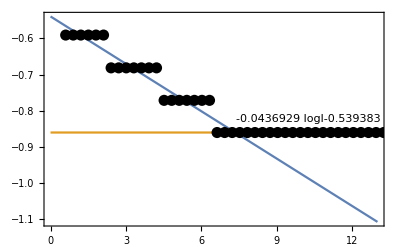

ΔD_q^Box=-0.00229962 ΔD_q^(asym)=0.00510509

```mathematica
xi=2;xf=xi+15;
fit1=LinearModelFit[Log10@dat[[xi;;xf]],logl,logl];

xi=22;xf=xi+38;
fit2=LinearModelFit[Log10@scaledat[[xi;;xf]],logl,logl];
Plot[{Normal@fit1,Normal@fit2},{logl,0,13},Axes->False,Frame->True,Epilog->{PointSize@.02,Point@Log10@dat},PlotLegends->Placed[Normal@fit1,{Right,Center}]]

(* renormalization path of the site *)
x=t[[i]]/n;
(* comparison with asymptotics *)
Print["ΔD_q^Box=",fit1[[1,2,2]]/(q-1)," ΔD_q^(asym)=",α[x] q/(q-1)(4-5 x)/6 ρ^2/Log[Fibonacci[n]^(1/n)]]
```